0.

9.90683

12.1413

13.0279

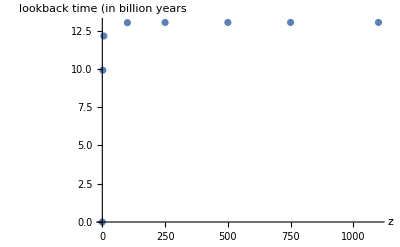

```mathematica
(* (i) Flat Lambda Cold Dark Matter model *)
Subscript[Ω, m]=0.3;
Subscript[Ω, r]=0;
Subscript[Ω, Λ]=0.7;
H[z_]:=0.074 √(Subscript[Ω, m](1+z)^3+Subscript[Ω, r](1+z)^4+Subscript[Ω, Λ]);
NIntegrate[1/H[z] 1/(1+z),{z,0,0}]
NIntegrate[1/H[z] 1/(1+z),{z,0,2}]
NIntegrate[1/H[z] 1/(1+z),{z,0,6}]
NIntegrate[1/H[z] 1/(1+z),{z,0,1100}]
ListPlot[{{0,NIntegrate[1/H[z] 1/(1+z),{z,0,0}]},
{2,NIntegrate[1/H[z] 1/(1+z),{z,0,2}]},
{6,NIntegrate[1/H[z] 1/(1+z),{z,0,6}]},
{100,NIntegrate[1/H[z] 1/(1+z),{z,0,100}]},
{250,NIntegrate[1/H[z] 1/(1+z),{z,0,250}]},{500,NIntegrate[1/H[z] 1/(1+z),{z,0,500}]},
{750,NIntegrate[1/H[z] 1/(1+z),{z,0,750}]},
{1100,NIntegrate[1/H[z] 1/(1+z),{z,0,1100}]}},AxesLabel->{"z","lookback time (in billion years"}]
```

0.

9.27786

11.4239

12.3045

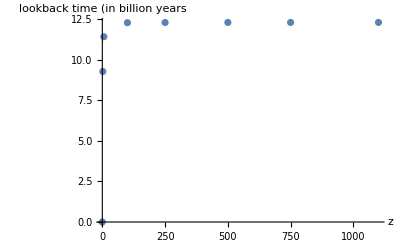

```mathematica
(* (ii) Flat dark energy (with an equation of state Subscript[w, DE]=−0.7 *)
Subscript[Ω, m]=0.3;
Subscript[Ω, r]=0;
Subscript[Ω, Λ]=0.7;
H[z_]:=0.074 √(Subscript[Ω, m](1+z)^3+Subscript[Ω, r](1+z)^4+Subscript[Ω, Λ](1+z)^0.9);
NIntegrate[1/H[z] 1/(1+z),{z,0,0}]
NIntegrate[1/H[z] 1/(1+z),{z,0,2}]
NIntegrate[1/H[z] 1/(1+z),{z,0,6}]
NIntegrate[1/H[z] 1/(1+z),{z,0,1100}]
ListPlot[{{0,NIntegrate[1/H[z] 1/(1+z),{z,0,0}]},
{2,NIntegrate[1/H[z] 1/(1+z),{z,0,2}]},
{6,NIntegrate[1/H[z] 1/(1+z),{z,0,6}]},
{100,NIntegrate[1/H[z] 1/(1+z),{z,0,100}]},
{250,NIntegrate[1/H[z] 1/(1+z),{z,0,250}]},{500,NIntegrate[1/H[z] 1/(1+z),{z,0,500}]},
{750,NIntegrate[1/H[z] 1/(1+z),{z,0,750}]},
{1100,NIntegrate[1/H[z] 1/(1+z),{z,0,1100}]}},AxesLabel->{"z","lookback time (in billion years"}]
```

0.

10.2436

12.5008

13.3881

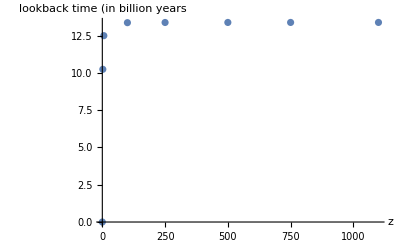

```mathematica
(* (iii) Flat dark energy (with an equation of state Subscript[w, DE]=−1.2 *)
Subscript[Ω, m]=0.3;
Subscript[Ω, r]=0;
Subscript[Ω, Λ]=0.7;
H[z_]:=0.074 √(Subscript[Ω, m](1+z)^3+Subscript[Ω, r](1+z)^4+Subscript[Ω, Λ](1+z)^-0.6);
NIntegrate[1/H[z] 1/(1+z),{z,0,0}]
NIntegrate[1/H[z] 1/(1+z),{z,0,2}]
NIntegrate[1/H[z] 1/(1+z),{z,0,6}]
NIntegrate[1/H[z] 1/(1+z),{z,0,1100}]
ListPlot[{{0,NIntegrate[1/H[z] 1/(1+z),{z,0,0}]},
{2,NIntegrate[1/H[z] 1/(1+z),{z,0,2}]},
{6,NIntegrate[1/H[z] 1/(1+z),{z,0,6}]},
{100,NIntegrate[1/H[z] 1/(1+z),{z,0,100}]},
{250,NIntegrate[1/H[z] 1/(1+z),{z,0,250}]},{500,NIntegrate[1/H[z] 1/(1+z),{z,0,500}]},
{750,NIntegrate[1/H[z] 1/(1+z),{z,0,750}]},
{1100,NIntegrate[1/H[z] 1/(1+z),{z,0,1100}]}},AxesLabel->{"z","lookback time (in billion years"}]
```

0.

7.75844

9.1501

9.69362

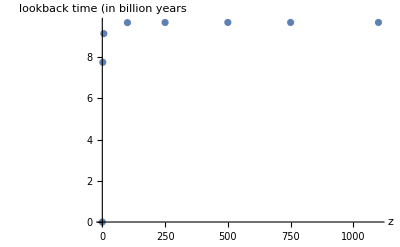

```mathematica
(* (iv) Flat Lambda Cold Dark Matter model with Subscript[Ω, m]=0.8 *)
Subscript[Ω, m]=0.8;
Subscript[Ω, r]=0;
Subscript[Ω, Λ]=0.2;
H[z_]:=0.074 √(Subscript[Ω, m](1+z)^3+Subscript[Ω, r](1+z)^4+Subscript[Ω, Λ]);
NIntegrate[1/H[z] 1/(1+z),{z,0,0}]
NIntegrate[1/H[z] 1/(1+z),{z,0,2}]
NIntegrate[1/H[z] 1/(1+z),{z,0,6}]
NIntegrate[1/H[z] 1/(1+z),{z,0,1100}]
ListPlot[{{0,NIntegrate[1/H[z] 1/(1+z),{z,0,0}]},
{2,NIntegrate[1/H[z] 1/(1+z),{z,0,2}]},
{6,NIntegrate[1/H[z] 1/(1+z),{z,0,6}]},
{100,NIntegrate[1/H[z] 1/(1+z),{z,0,100}]},
{250,NIntegrate[1/H[z] 1/(1+z),{z,0,250}]},{500,NIntegrate[1/H[z] 1/(1+z),{z,0,500}]},
{750,NIntegrate[1/H[z] 1/(1+z),{z,0,750}]},
{1100,NIntegrate[1/H[z] 1/(1+z),{z,0,1100}]}},AxesLabel->{"z","lookback time (in billion years"}]
```